```mathematica
用硬算的频谱振幅和相位来恢复轨道,窗口时间要正确使用才能恢复信号振幅
```

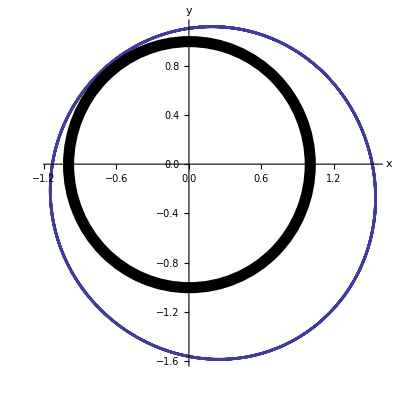

```mathematica
τ=200;
x=59.5715/τ+
(132.812 Sin[2π×0.625969 t-0.257694]+
15.2122 Sin[2π×1.25199 t+0.133914]+
2.5713 Sin[2π×1.87776 t+0.637626])×2/τ;
y=-72.2912/τ+
(133.28 Sin[2π× 0.625966 t+1.32633]+
15.1063 Sin[2π×1.25199 t+1.71]+
2.48029 Sin[2π×1.878 t+2.07188])×2/τ;
ParametricPlot[{x,y},{t,0,5},
AxesLabel->{"x","y"},
Epilog->{Thickness[0.02],Circle[{0,0},1]},
PlotStyle->Thickness[0.005],
AxesStyle->Thickness[0.005]]
Clear[τ,x,y,t]
```